## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="TRPS3";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_trp3.csv";

mainFolder = "fit_TRPS3_TEST_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName,  assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{3ig3p,Null;,Keq substrate}

{0.00043,Keq value}

{{{3ig3p,Null}},kcat substrates}

{0.48,kcat value}

{3ig3p,Other parameter susbtrate}

{1040,Other parameter value}

{3ig3p,Km or S05 substrate}

{0.00046,Km or S05 value}

{{{3ig3p,Null}},kcat substrates}

{0.005,kcat value}

{3ig3p,Km or S05 substrate}

{0.00025,Km or S05 value}

{3ig3p,Other parameter susbtrate}

{20,Other parameter value}

((3ig3p)^c⇌g3p^c+indole^c)^TRPS3

Uni-bi;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3ig3p,Null; | 0.00043 | 0.0004085
0.0004515 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3ig3p | 0.00046 | 0.000437
0.000483 |  | M | 7.8 | 37 | trishcl | 0.005 | na1 | 0.18
cl | 0.18
1 | 3ig3p | 0.00025 | 0.0002375
0.0002625 |  | M | 7.8 | 37 | trishcl | 0.005
edta | 0.004 | na1 | 0.18
cl | 0.18

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3ig3p | Null | 0.48 | 0.456
0.504 | 1/s | 7.8 | 37 | trishcl | 0.005 | na1 | 0.18
cl | 0.18
1 | 3ig3p | Null | 0.005 | 0.00475
0.00525 | 1/s | 7.8 | 37 | trishcl | 0.005
edta | 0.004 | na1 | 0.18
cl | 0.18

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | kcat/Km | 3ig3p | 1040 | 988
1092 |  | 1/(s*M) | 7.8 | 37 | trishcl | 0.005 | na1 | 0.18
cl | 0.18
1 | kcat/Km | 3ig3p | 20 | 19
21 |  | 1/(s*M) | 7.8 | 37 | trishcl | 0.005
edta | 0.004 | na1 | 0.18
cl | 0.18

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {0.7,0.5};
s05Priorities = Null;
kcatPriorities = {0.7,0.5};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = {0,0};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((3ig3p)^c⇌g3p^c+indole^c)^TRPS3

Uni-bi;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3ig3p,Null; | 0.00043 | 0.0004085
0.0004515 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
0.7 | 3ig3p | 0.00046 | 0.000437
0.000483 |  | M | 7.8 | 37 | trishcl | 0.005 | na1 | 0.18
cl | 0.18
0.5 | 3ig3p | 0.00025 | 0.0002375
0.0002625 |  | M | 7.8 | 37 | trishcl | 0.005
edta | 0.004 | na1 | 0.18
cl | 0.18

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
0.7 | 3ig3p | Null | 0.48 | 0.456
0.504 | 1/s | 7.8 | 37 | trishcl | 0.005 | na1 | 0.18
cl | 0.18
0.5 | 3ig3p | Null | 0.005 | 0.00475
0.00525 | 1/s | 7.8 | 37 | trishcl | 0.005
edta | 0.004 | na1 | 0.18
cl | 0.18

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_TRPS3[c] + 3ig3p[c] <=> E_TRPS3[c]&3ig3p",
				"E_TRPS3[c]&3ig3p <=> E_TRPS3[c]&indole&g3p",
				"E_TRPS3[c]&indole&g3p <=> E_TRPS3[c]&indole + g3p[c]",
				"E_TRPS3[c]&indole <=> E_TRPS3[c] + indole[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((TRPS3^c)_^+(3ig3p)^c⇌(TRPS3^c&(3ig3p)^c)_^)^TRPS31,((TRPS3^c&indole^c)_^⇌(TRPS3^c)_^+indole^c)^TRPS32,((TRPS3^c&(3ig3p)^c)_^⇌(TRPS3^c&indole^c&g3p^c)_^)^TRPS33,((TRPS3^c&indole^c&g3p^c)_^⇌(TRPS3^c&indole^c)_^+g3p^c)^TRPS34}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((TRPS3^c)_^+(3ig3p)^c⇌(TRPS3^c&(3ig3p)^c)_^)^TRPS31,Overscript[(TRPS3^c&indole^c)_^⇌(TRPS3^c)_^+indole^c, TRPS32],((TRPS3^c&(3ig3p)^c)_^⇌(TRPS3^c&indole^c&g3p^c)_^)^TRPS33,Overscript[(TRPS3^c&indole^c&g3p^c)_^⇌(TRPS3^c&indole^c)_^+g3p^c, TRPS34]};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{(3ig3p)^c→0}

{g3p^c→0,indole^c→0}

{(3ig3p)^c→∞}

{g3p^c→∞,indole^c→∞}

Added inhibition reactions:

{}

Generating flux equation...

{((TRPS3^c&(3ig3p)^c)_^-((TRPS3^c&indole^c&g3p^c)_^)/K_TRPS33) Volume_c k_TRPS33^⟶}

Volume_c (-(TRPS3^c&indole^c&g3p^c)_^ k_TRPS33^⟵+(TRPS3^c&(3ig3p)^c)_^ k_TRPS33^⟶)

1

2

3

0.10819

4

0.000523

5

0.00014

Simplifying...

6

0.076488

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={(*{1, (Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶Subscript[k, GAPD5]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵Subscript[k, GAPD5]^⟵), 4.25*10^2,{0.9*4.25*10^2,1.1*4.25*10^2}}*)};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
Print[bufferInfo]
```

{{{trishcl,Tris-HCl},8.14,1,0},{{tris,Tris},8.14,1,0},{{trisac,Tris-acetate},8.14,1,0},{{edta,EDTA},Null,Null,Null},{{tric,Tricine},8.07,0,-1},{{tricna,Tricine-Na},8.07,0,-1},{{hepesnaoh,Hepes-NaOH},7.5,0,-1},{{pipeskoh,PIPES-KOH},6.64,-1,-2},{{kpi,KPO4},6.88,-1,-2},{{napi,sodium phosphate},6.88,-1,-2},{{nakpi,Na+/K+ phosphate},6.88,-1,-2},{{chesk,CHES-K},9.37,0,-1},{{hepes,Hepes},7.5,0,-1},{{hepesbtp,HEPES-BTP},Null,Null,Null},{{pipes,Pipes},6.64,-1,-2},{{mops,MOPS},7.12,0,-1},{{mopsnaoh,MOPS/NaOH},7.12,0,-1},{{mopskoh,MOPS-KOH},7.12,0,-1},{{mes,MES},6.14,0,-1},{{netmphn,N-ethylmorpholine},7.83,1,0},{{detam,diethanolamine},8.95,1,0},{{glygly,glycylglycine},8.2,0,-1},{{imdzcl,imidazole-Cl},7.06,1,0},{{imdz_MIXED,mixed imidazoles},Null,Null,Null},{{24dmid,2,4-dimethylimidazole},Null,Null,Null},{{teoa,triethanolamine},7.83,1,0},{{teoahcl,triethanolamine-HCl},7.83,1,0},{{pi_buffer,Phosphoric acid},7.198,-1,-2}}

```mathematica
Print[bufferInfo]
```

{{{trishcl,Tris-HCl},8.14,1,0},{{tris,Tris},8.14,1,0},{{trisac,Tris-acetate},8.14,1,0},{{edta,EDTA},Null,Null,Null},{{tric,Tricine},8.07,0,-1},{{tricna,Tricine-Na},8.07,0,-1},{{hepesnaoh,Hepes-NaOH},7.5,0,-1},{{pipeskoh,PIPES-KOH},6.64,-1,-2},{{kpi,KPO4},6.88,-1,-2},{{napi,sodium phosphate},6.88,-1,-2},{{nakpi,Na+/K+ phosphate},6.88,-1,-2},{{chesk,CHES-K},9.37,0,-1},{{hepes,Hepes},7.5,0,-1},{{hepesbtp,HEPES-BTP},Null,Null,Null},{{pipes,Pipes},6.64,-1,-2},{{mops,MOPS},7.12,0,-1},{{mopsnaoh,MOPS/NaOH},7.12,0,-1},{{mopskoh,MOPS-KOH},7.12,0,-1},{{mes,MES},6.14,0,-1},{{netmphn,N-ethylmorpholine},7.83,1,0},{{detam,diethanolamine},8.95,1,0},{{glygly,glycylglycine},8.2,0,-1},{{imdzcl,imidazole-Cl},7.06,1,0},{{imdz_MIXED,mixed imidazoles},Null,Null,Null},{{24dmid,2,4-dimethylimidazole},Null,Null,Null},{{teoa,triethanolamine},7.83,1,0},{{teoahcl,triethanolamine-HCl},7.83,1,0},{{pi_buffer,Phosphoric acid},7.198,-1,-2}}

```mathematica
FilePrint@dataPathList
```

Priority	3ig3p[c]	g3p[c]	indole[c]	param_TRPS3_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/haldaneRatio_1.txt"	0.00043
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/haldaneRatio_1.txt"	0.00043
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/haldaneRatio_1.txt"	0.00043
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/haldaneRatio_1.txt"	0.00043
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/haldaneRatio_1.txt"	0.00043
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/haldaneRatio_1.txt"	0.00043
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/haldaneRatio_1.txt"	0.00043
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/haldaneRatio_1.txt"	0.00043
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/haldaneRatio_1.txt"	0.00043
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/haldaneRatio_1.txt"	0.00043
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/haldaneRatio_1.txt"	0.00043
0.7	0.00004600000000000003	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.09090909090909095
0.7	0.00007290508685321129	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.1368068886032101
0.7	0.00011554677584944073	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.2007600089131018
0.7	0.00018312929845460887	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.28474724895080156
0.7	0.0002902403784608889	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.386863179846857
0.7	0.00046000000000000023	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.5000000000000001
0.7	0.000729050868532113	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.6131368201531432
0.7	0.0011554677584944084	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.7152527510491988
0.7	0.0018312929845460887	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.7992399910868985
0.7	0.0029024037846088896	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.86319311139679
0.7	0.0046000000000000025	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.9090909090909091
0.5	0.000024999999999999994	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.09090909090909088
0.5	0.00003962232981152784	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.13680688860321003
0.5	0.00006279716078773954	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.20076000891310186
0.5	0.0000995267926383742	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.28474724895080117
0.5	0.00015773933612004822	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.3868631798468568
0.5	0.00024999999999999995	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.4999999999999999
0.5	0.0003962232981152784	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.6131368201531431
0.5	0.0006279716078773954	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.7152527510491987
0.5	0.0009952679263837431	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.7992399910868982
0.5	0.0015773933612004821	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.8631931113967899
0.5	0.002499999999999999	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt"	0.9090909090909092
0.7	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.48
0.7	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.48
0.7	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.48
0.7	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.48
0.7	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.48
0.7	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.48
0.7	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.48
0.7	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.48
0.7	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.48
0.7	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.48
0.7	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.48
0.5	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.005
0.5	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.005
0.5	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.005
0.5	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.005
0.5	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.005
0.5	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.005
0.5	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.005
0.5	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.005
0.5	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.005
0.5	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.005
0.5	0.01	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt"	0.005

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateRev_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateRev_indole.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateFor_3ig3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateRev_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/relRateRev_indole.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 7.19917375711
best_fit: 7.19917376956
best_fit: 7.19917377419
best_fit: 7.19917375634
best_fit: 7.19917382512

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/TRPS3.dat⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.0000177459 | 3.14916×10^-10 | 1.757×10^-8 | 0.00408606 | 0.00043 | 0.000429982
1 | haldaneRatio_1 | 0.0000177459 | 3.14916×10^-10 | 1.757×10^-8 | 0.00408606 | 0.00043 | 0.000429982
1 | haldaneRatio_1 | 0.0000177459 | 3.14916×10^-10 | 1.757×10^-8 | 0.00408606 | 0.00043 | 0.000429982
1 | haldaneRatio_1 | 0.0000177459 | 3.14916×10^-10 | 1.757×10^-8 | 0.00408606 | 0.00043 | 0.000429982
1 | haldaneRatio_1 | 0.0000177459 | 3.14916×10^-10 | 1.757×10^-8 | 0.00408606 | 0.00043 | 0.000429982
1 | haldaneRatio_1 | 0.0000177459 | 3.14916×10^-10 | 1.757×10^-8 | 0.00408606 | 0.00043 | 0.000429982
1 | haldaneRatio_1 | 0.0000177459 | 3.14916×10^-10 | 1.757×10^-8 | 0.00408606 | 0.00043 | 0.000429982
1 | haldaneRatio_1 | 0.0000177459 | 3.14916×10^-10 | 1.757×10^-8 | 0.00408606 | 0.00043 | 0.000429982
1 | haldaneRatio_1 | 0.0000177459 | 3.14916×10^-10 | 1.757×10^-8 | 0.00408606 | 0.00043 | 0.000429982
1 | haldaneRatio_1 | 0.0000177459 | 3.14916×10^-10 | 1.757×10^-8 | 0.00408606 | 0.00043 | 0.000429982
1 | haldaneRatio_1 | 0.0000177459 | 3.14916×10^-10 | 1.757×10^-8 | 0.00408606 | 0.00043 | 0.000429982
0.7 | relRateFor_3ig3p | 0.0930203 | 0.00865278 | 0.0217141 | 23.8855 | 0.0909091 | 0.112623
0.7 | relRateFor_3ig3p | 0.0878144 | 0.00771137 | 0.0306575 | 22.4093 | 0.136807 | 0.167464
0.7 | relRateFor_3ig3p | 0.0806631 | 0.00650654 | 0.0409754 | 20.4102 | 0.20076 | 0.241735
0.7 | relRateFor_3ig3p | 0.0714469 | 0.00510466 | 0.0509181 | 17.8818 | 0.284747 | 0.335665
0.7 | relRateFor_3ig3p | 0.0604987 | 0.00366009 | 0.0578255 | 14.9473 | 0.386863 | 0.444689
0.7 | relRateFor_3ig3p | 0.0486826 | 0.00237 | 0.0593101 | 11.862 | 0.5 | 0.55931
0.7 | relRateFor_3ig3p | 0.0371796 | 0.00138232 | 0.0548025 | 8.93805 | 0.613137 | 0.667939
0.7 | relRateFor_3ig3p | 0.0270524 | 0.000731832 | 0.0459703 | 6.42714 | 0.715253 | 0.761223
0.7 | relRateFor_3ig3p | 0.0188965 | 0.000357078 | 0.0355432 | 4.44713 | 0.79924 | 0.834783
0.7 | relRateFor_3ig3p | 0.0127872 | 0.000163513 | 0.0257934 | 2.98814 | 0.863193 | 0.888987
0.7 | relRateFor_3ig3p | 0.00845509 | 0.0000714885 | 0.0178721 | 1.96593 | 0.909091 | 0.926963
0.5 | relRateFor_3ig3p | 0.148874 | 0.0221634 | 0.0263833 | 29.0216 | 0.0909091 | 0.0645258
0.5 | relRateFor_3ig3p | 0.142463 | 0.0202958 | 0.0382596 | 27.9661 | 0.136807 | 0.0985473
0.5 | relRateFor_3ig3p | 0.13337 | 0.0177876 | 0.053085 | 26.442 | 0.20076 | 0.147675
0.5 | relRateFor_3ig3p | 0.121132 | 0.014673 | 0.0693066 | 24.3397 | 0.284747 | 0.215441
0.5 | relRateFor_3ig3p | 0.105772 | 0.0111877 | 0.0836239 | 21.6159 | 0.386863 | 0.303239
0.5 | relRateFor_3ig3p | 0.0880948 | 0.0077607 | 0.091798 | 18.3596 | 0.5 | 0.408202
0.5 | relRateFor_3ig3p | 0.0696675 | 0.00485356 | 0.090873 | 14.821 | 0.613137 | 0.522264
0.5 | relRateFor_3ig3p | 0.052336 | 0.00273906 | 0.0812028 | 11.353 | 0.715253 | 0.63405
0.5 | relRateFor_3ig3p | 0.0375441 | 0.00140956 | 0.0661909 | 8.28173 | 0.79924 | 0.733049
0.5 | relRateFor_3ig3p | 0.0259328 | 0.000672509 | 0.0500347 | 5.79646 | 0.863193 | 0.813158
0.5 | relRateFor_3ig3p | 0.017404 | 0.000302898 | 0.0357107 | 3.92818 | 0.909091 | 0.87338
0.7 | absRateFor | 0.669626 | 0.448398 | 0.377289 | 78.6019 | 0.48 | 0.102711
0.7 | absRateFor | 0.669626 | 0.448398 | 0.377289 | 78.6019 | 0.48 | 0.102711
0.7 | absRateFor | 0.669626 | 0.448398 | 0.377289 | 78.6019 | 0.48 | 0.102711
0.7 | absRateFor | 0.669626 | 0.448398 | 0.377289 | 78.6019 | 0.48 | 0.102711
0.7 | absRateFor | 0.669626 | 0.448398 | 0.377289 | 78.6019 | 0.48 | 0.102711
0.7 | absRateFor | 0.669626 | 0.448398 | 0.377289 | 78.6019 | 0.48 | 0.102711
0.7 | absRateFor | 0.669626 | 0.448398 | 0.377289 | 78.6019 | 0.48 | 0.102711
0.7 | absRateFor | 0.669626 | 0.448398 | 0.377289 | 78.6019 | 0.48 | 0.102711
0.7 | absRateFor | 0.669626 | 0.448398 | 0.377289 | 78.6019 | 0.48 | 0.102711
0.7 | absRateFor | 0.669626 | 0.448398 | 0.377289 | 78.6019 | 0.48 | 0.102711
0.7 | absRateFor | 0.669626 | 0.448398 | 0.377289 | 78.6019 | 0.48 | 0.102711
0.5 | absRateFor | 1.31265 | 1.72304 | 0.0977107 | 1954.21 | 0.005 | 0.102711
0.5 | absRateFor | 1.31265 | 1.72304 | 0.0977107 | 1954.21 | 0.005 | 0.102711
0.5 | absRateFor | 1.31265 | 1.72304 | 0.0977107 | 1954.21 | 0.005 | 0.102711
0.5 | absRateFor | 1.31265 | 1.72304 | 0.0977107 | 1954.21 | 0.005 | 0.102711
0.5 | absRateFor | 1.31265 | 1.72304 | 0.0977107 | 1954.21 | 0.005 | 0.102711
0.5 | absRateFor | 1.31265 | 1.72304 | 0.0977107 | 1954.21 | 0.005 | 0.102711
0.5 | absRateFor | 1.31265 | 1.72304 | 0.0977107 | 1954.21 | 0.005 | 0.102711
0.5 | absRateFor | 1.31265 | 1.72304 | 0.0977107 | 1954.21 | 0.005 | 0.102711
0.5 | absRateFor | 1.31265 | 1.72304 | 0.0977107 | 1954.21 | 0.005 | 0.102711
0.5 | absRateFor | 1.31265 | 1.72304 | 0.0977107 | 1954.21 | 0.005 | 0.102711
0.5 | absRateFor | 1.31265 | 1.72304 | 0.0977107 | 1954.21 | 0.005 | 0.102711

### Simulated Data and Best Fit Data Plot

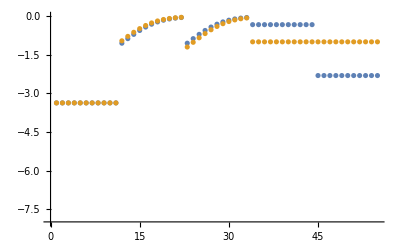

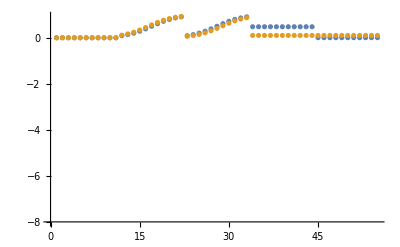

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

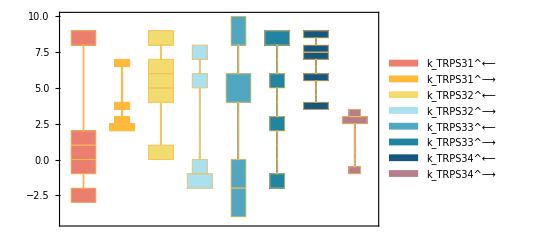

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

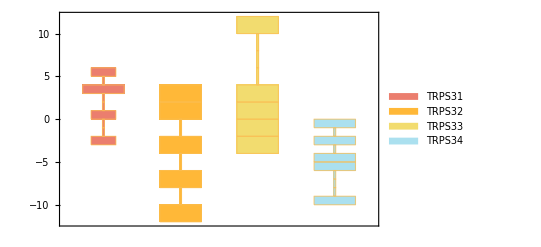

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

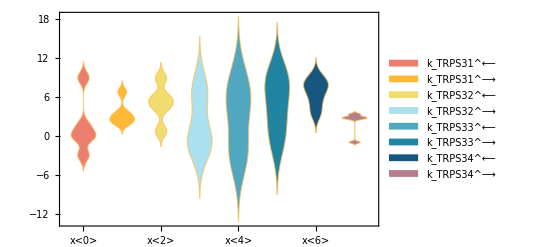

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

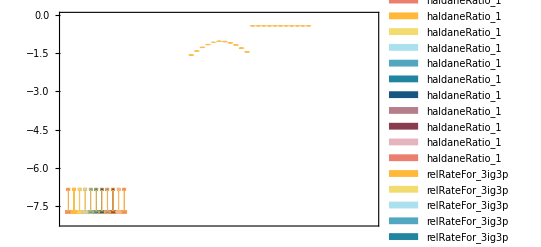

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.00046 | 0.000362442 | 21.2083
0.00025 | 0.000362442 | 44.9767

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
0.48 | 0.102711 | 78.6019
0.005 | 0.102711 | 1954.21

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

data value | predicted value | error in %
{}⟦1⟧⟦3⟧ | 1 | (100 Abs[-1+{}⟦1⟧⟦3⟧])/({}⟦1⟧⟦3⟧)

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.00043 | 0.000429982 | 0.00408606